# A simple model for actin polymerization explored by Gillespie simulation and Master Equation Modeling

## Matt Bovyn (mbovyn@uci.edu) MCSB Bootcamp 2018 Inspired by: http://www.rpgroup.caltech.edu/mbl_physiology/code/cytoskeleton_manual.html

## Actin

The actin cytoskeleton is a dynamic mesh, responsible for cell structure and movement

-Graphics-
Xu ... Zhuang Nature Methods 2012
https://www.nature.com/articles/nmeth.1841

Examples of dynamic actin protrusions and motility:
Fritz-Laylin ... Mullins, eLife 2017
https://elifesciences.org/articles/26990
-Graphics-

Actin (with only minimal helpers: salts, etc.) forms a double helical polymer

-Graphics-
http://www.spring8.or.jp/en/news_publications/press_release/2009/090122/

## How long is an actin filament?

Let’s make a minimal model. We know:
1. Actin polymerizes - adds monomers
2. Actin depolymerizes - monomers fall off
3. This process is dynamic

For any one filament, length is a function of time. Let’s make a simple model where monomers pop on and off with equal probability, then plot a stochastic trajectory

```mathematica
lengthWithTime[nsteps_]:=Module[{currentL,history,change},
currentL=5;
history={{0,currentL}};
Do[change=RandomChoice[{-1,1}];
currentL=currentL+change;
If[currentL<1,currentL=1];
AppendTo[history,{i,currentL}];
,{i,1,nsteps}];
history]
```

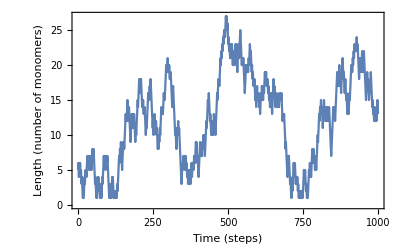

```mathematica
ListLinePlot[lengthWithTime[1000],Frame->True,FrameLabel->{"Time (steps)","Length (number of monomers)"}]
```

How long is it? Look at distribution of lengths

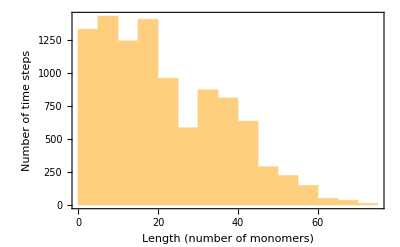

```mathematica
simpletraj=lengthWithTime[10000];
Histogram[simpletraj[[All,2]],Frame->True,FrameLabel->{"Length (number of monomers)","Number of time steps"}]
```

Hard to tell what the distribution is, things turn out different each time.

## A more physical model for length dynamics & Gillespie

If we are going to make a real model, we want output of length vs. time in seconds. For this, our model also needs to have physical parameters, which also have units.

We can phrase how often monomers go onto the filament as a rate (measured in inverse seconds), and the same for how often they fall off. We call them the on rate (kon) and the off rate (koff).

With these parameters in mind, we can use a framework centered around the Gillespie algorithm to simulate time courses of the length of the filament. The Gillespie algorithm is a general way to simulate stochastic trajectories of chemical reactions when you know the rates of those reactions.

For Gillespie, we first need to be able to pull random numbers from an exponential distribution. We do that by

```mathematica
RandomVariate[ExponentialDistribution[3]]
```

0.211247

but we see that the mean of generated numbers is

```mathematica
Mean[RandomVariate[ExponentialDistribution[3],10000]]
```

0.330096

the inverse of the number we give ExponentialDistribution. So, if we put in a rate in (1/seconds), we get out a time (in seconds).

Then, to do a Gillespie simulation, we
1. choose initial length and time
2. Generate exponential random times from the distributions for each rate (kon and koff)
3. Choose the smaller of the two generated times. Increment our timestep by this time, then take the appropriate action (length+1, length-1)

```mathematica
lengthWithTimeGillespie[nsteps_,kon_,koff_]:=Module[{currentL,history,change,konrand,koffrand,t,dt},
currentL=5;
t=0;
history={{t,currentL}};
Do[konrand=RandomVariate[ExponentialDistribution[kon]];
koffrand=RandomVariate[ExponentialDistribution[koff]];
If[konrand<koffrand,
change=1;dt=konrand;,
change=-1;,dt=koffrand;];
currentL=currentL+change;
t=t+dt;
If[currentL<1,currentL=1];
AppendTo[history,{t,currentL}];
,{i,1,nsteps}];
history]
```

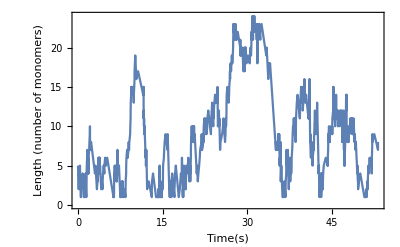

```mathematica
ListLinePlot[lengthWithTimeGillespie[1000,9,10],Frame->True,FrameLabel->{"Time(s)","Length (number of monomers)"}]
```

We now see that for the case of kon<koff, we get an exponential distribution of lengths for actin filaments

```mathematica
gillespietraj=lengthWithTimeGillespie[10000,9,10];
```

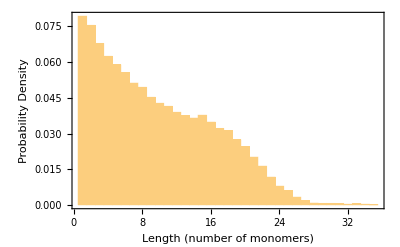

```mathematica
Histogram[gillespietraj[[All,2]],Automatic,"PDF",Frame->True,FrameLabel->{"Length (number of monomers)","Probability Density"}]
```

If the on rate is higher than the off rate, we find an approximately uniform distribution

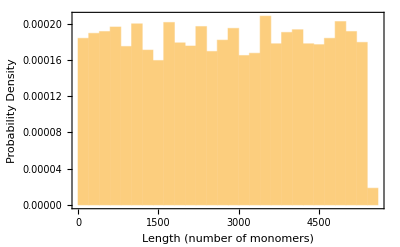

```mathematica
gillespietrajsr=lengthWithTimeGillespie[10000,10,3];
Histogram[gillespietrajsr[[All,2]],Automatic,"PDF",Frame->True,FrameLabel->{"Length (number of monomers)","Probability Density"}]
```

In the case where the two rates are equal, we find that our Gillespie scheme gives similar results to the simple simulation we wrote at the start.

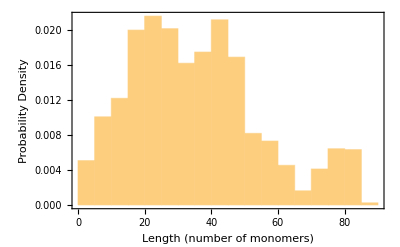

```mathematica
gillespietrajsr=lengthWithTimeGillespie[10000,1,1];
Histogram[gillespietrajsr[[All,2]],Automatic,"PDF",Frame->True,FrameLabel->{"Length (number of monomers)","Probability Density"}]
```

## Master equation for actin length

Another way to investigate the distribution of lengths is to write down differential equations for the probability of being at each  length. This is called writing down the master equation. We do that by:

prob at next time = prob at last time + probability in - probability out
for a filament with 3 monomers 
prob at next time = prob at last time + 2 gained one + 4 lost one - 3 gained one - 3 lost one 
P[l=3,t+Δt]=P[l=3,t]+kon Δt  P[l=2,t] + koff Δt P[l=4,t] -kon Δt P[l=3,t] - koff Δt P[l=3,t] 

P[l,t+Δt]=P[l,t]+kon Δt  P[l-1,t] + koff Δt P[l+1,t] -(kon +koff) Δt P[l,t]

This is the discretized form of a set of coupled differential equations, one for probability of each number of monomers. We can then solve the equations forward in time.

```mathematica
forwardEulerSolve[kon_,koff_,dt_,lmax_,tsteps_]:=Module[{t,p,l},
p=ConstantArray[{0,0},{lmax,tsteps}];
p[[1,1]][[2]]=1;
For[t=2,t<=tsteps,t++,
p[[1,t]][[2]]=p[[1,t-1]][[2]]+koff dt p[[2,t-1]][[2]]-kon dt p[[1,t-1]][[2]];
p[[lmax,t]][[2]]=p[[lmax,t-1]][[2]]+kon dt p[[lmax-1,t-1]][[2]]-koff dt p[[lmax,t-1]][[2]];
For[l=2,l<lmax,l++,
p[[l,t]][[2]]=p[[l,t-1]][[2]]+kon dt p[[l-1,t-1]][[2]]+koff dt p[[l+1,t-1]][[2]] -(kon+koff) dt p[[l,t-1]][[2]];
];
For[l=1,l<=lmax,l++,p[[l,t]][[1]]=dt (t-1);];
];
p]
```

```mathematica
numans=forwardEulerSolve[9,10,N[1/50],30,500];
```

Then we can look at how the probabilities evolve in time. (Colors indicate different numbers of monomers)

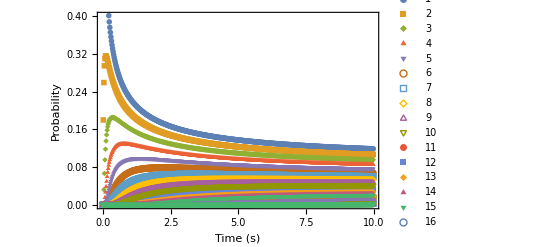

```mathematica
ListPlot[numans,PlotRange->{0,.4},PlotMarkers->{Automatic,Small},Frame->True,FrameLabel->{"Time (s)","Probability"},PlotLegends->Range[1,Dimensions[numans,1]]]
```

We see they reach a steady state. The steady state distribution is exponential, like before

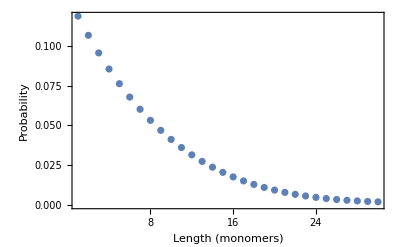

```mathematica
ListPlot[numans[[All,-1,2]],PlotRange->All,Frame->True,FrameLabel->{"Length (monomers)","Probability"}]
```

## Numerical solution the Mathematica way

Write down a set of ODEs analogous to the one above (but not discretized)
ⅆP[l_n]/ⅆt=kon P_(n-1) + koff  P_(n+1) -(kon +koff) P_n  
Keep in mind the first (1) and last (N) ones should be different!
ⅆP[l_1]/ⅆt= koff  P_(n+1) -(kon ) P_n  
ⅆP[l_N]/ⅆt=kon P_(N-1) -(koff) P_n

These are many equations, one for each value of l. Write them all out using Mathematica

```mathematica
writeEqs[numLs_]:=Module[{lst,coeffs,ics},
(*list of equations*)
lst=Table[If[k==1,D[p[k][t],t]==koff p[k+1][t]-(kon)p[k][t],If[k==numLs,D[p[k][t],t]==-(koff)p[k][t]+kon p[k-1][t],D[p[k][t],t]==koff p[k+1][t]-(kon+koff)p[k][t]+kon p[k-1][t]]],{k,1,numLs}];
(*list of variables we want to solve for*)
coeffs=Table[p[k][t],{k,1,numLs}];
(*list of initial conditions*)
ics=#==0&/@coeffs;
ics=ics/.{p[1][t]==0->p[1][t]==1}/.t->0;
{lst,ics,coeffs}]
```

Perform the numerical solution

```mathematica
{lst,ics,coeffs}=writeEqs[50];
```

```mathematica
ndsolveans=NDSolve[Join[lst,ics]/.{kon->9,koff->10},coeffs,{t,0,10}];
```

We see that the probabilities are very similar to those we got from our own solver

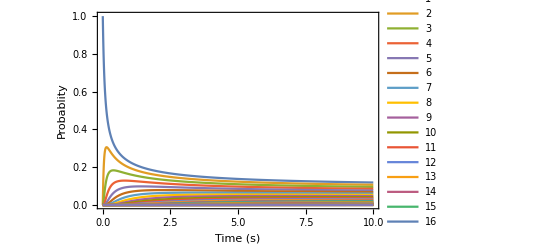

```mathematica
Plot[Evaluate[coeffs/.ndsolveans],{t,0,10},PlotRange->All,Frame->True,FrameLabel->{"Time (s)","Probablity"},PlotLegends->Range[1,Dimensions[lst,1]]]
```

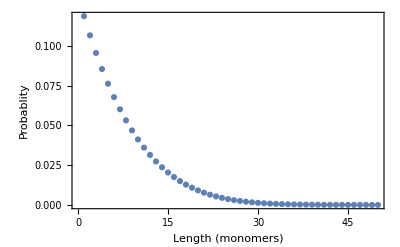

```mathematica
ListPlot[coeffs/.ndsolveans/.t->10,PlotRange->All,Frame->True,FrameLabel->{"Length (monomers)","Probablity"}]
```

## Broken down version of the stuff happening in the module above

Want to use NDSolve to solve our system of differential equations, so we needs a list of equations and a list of things we want to solve for

```mathematica
?NDSolve
```

NDSolve[eqns,u,{x,x_min,x_max}] finds a numerical solution to the ordinary differential equations eqns for the function u with the independent variable x in the range x_min to x_max. 
NDSolve[eqns,u,{x,x_min,x_max},{y,y_min,y_max}] solves the partial differential equations eqns over a rectangular region.
NDSolve[eqns,u,{x,y}∈Ω] solves the partial differential equations eqns over the region Ω.
NDSolve[eqns,u,{t,t_min,t_max},{x,y}∈Ω] solves the time-dependent partial differential equations eqns over the region Ω.
NDSolve[eqns,{u_1,u_2,…},…] solves for the functions u_i.

First, write out the differential equations

```mathematica
last=5;
lst=Table[If[k==1,D[p[k][t],t]==koff p[k+1][t]-(kon)p[k][t],If[k==last,D[p[k][t],t]==-(koff)p[k][t]+kon p[k-1][t],D[p[k][t],t]==koff p[k+1][t]-(kon+koff)p[k][t]+kon p[k-1][t]]],{k,1,last}]
```

{p[1]'[t]==-kon p[1][t]+koff p[2][t],p[2]'[t]==kon p[1][t]-(koff+kon) p[2][t]+koff p[3][t],p[3]'[t]==kon p[2][t]-(koff+kon) p[3][t]+koff p[4][t],p[4]'[t]==kon p[3][t]-(koff+kon) p[4][t]+koff p[5][t],p[5]'[t]==kon p[4][t]-koff p[5][t]}

Then write out the things we want to solve for

```mathematica
coeffs=Table[p[k][t],{k,1,last}]
```

{p[1][t],p[2][t],p[3][t],p[4][t],p[5][t]}

And finally the initial conditions, which are all 0 except the probability of having one monomer, which is one. Use map and pure function to write out each entry in coeffs == 0

```mathematica
ics=#==0&/@coeffs
```

{p[1][t]==0,p[2][t]==0,p[3][t]==0,p[4][t]==0,p[5][t]==0}

Then sub in 0 for time and set the probability of having one monomer to 1

```mathematica
ics=ics/.{p[1][t]==0->p[1][t]==1}/.t->0
```

{p[1][0]==1,p[2][0]==0,p[3][0]==0,p[4][0]==0,p[5][0]==0}

## Attempt at analytical solution

With the lists of equations generated above, we can also get the analytical solution when we use a low number of monomers

```mathematica
{lst,ics,coeffs}=writeEqs[3];
ans3=DSolve[Join[lst,ics],coeffs,t]
```

{{p[1][t]→(2 koff^2+ⅇ^((-koff-√koff √kon-kon) t) koff kon+ⅇ^((-koff+√koff √kon-kon) t) koff kon-ⅇ^((-koff-√koff √kon-kon) t) √koff kon^(3/2)+ⅇ^((-koff+√koff √kon-kon) t) √koff kon^(3/2)+ⅇ^((-koff-√koff √kon-kon) t) kon^2+ⅇ^((-koff+√koff √kon-kon) t) kon^2)/(2 (koff-√koff √kon+kon) (koff+√koff √kon+kon)),p[2][t]→-((kon (-2 koff^(3/2)+ⅇ^((-koff-√koff √kon-kon) t) koff^(3/2)+ⅇ^((-koff+√koff √kon-kon) t) koff^(3/2)+ⅇ^((-koff-√koff √kon-kon) t) kon^(3/2)-ⅇ^((-koff+√koff √kon-kon) t) kon^(3/2)))/(2 √koff (koff-√koff √kon+kon) (koff+√koff √kon+kon))),p[3][t]→(kon^(3/2) (ⅇ^((-koff-√koff √kon-kon) t) koff-ⅇ^((-koff+√koff √kon-kon) t) koff+2 √koff √kon-ⅇ^((-koff-√koff √kon-kon) t) √koff √kon-ⅇ^((-koff+√koff √kon-kon) t) √koff √kon+ⅇ^((-koff-√koff √kon-kon) t) kon-ⅇ^((-koff+√koff √kon-kon) t) kon))/(2 √koff (koff-√koff √kon+kon) (koff+√koff √kon+kon))}}

However, we can see its super nasty, even with only 3 equations. We can still make nice nice plot

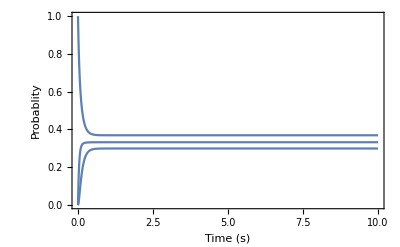

```mathematica
Plot[coeffs/.ans3/.{kon->9,koff->10}//Simplify,{t,0,10},PlotRange->All,Frame->True,FrameLabel->{"Time (s)","Probablity"}]
```

## Steady State

Write out the steady state version of the equations (where the derivative term is 0). Note these equations are algebraic.

```mathematica
{lst,ics,coeffs}=writeEqs[5];
```

```mathematica
lstss=lst/.p[_]'[t]->0
```

{0==-kon p[1][t]+koff p[2][t],0==kon p[1][t]-(koff+kon) p[2][t]+koff p[3][t],0==kon p[2][t]-(koff+kon) p[3][t]+koff p[4][t],0==kon p[3][t]-(koff+kon) p[4][t]+koff p[5][t],0==kon p[4][t]-koff p[5][t]}

Solve for the rest of the coefficients in terms of the first one

```mathematica
ssans=Solve[lstss,Rest[coeffs]]//First
```

{p[2][t]→(kon p[1][t])/koff,p[3][t]→(kon^2 p[1][t])/koff^2,p[4][t]→(kon^3 p[1][t])/koff^3,p[5][t]→(kon^4 p[1][t])/koff^4}

Since these are probabilities, they must sum to 1. This gives another equation, which we can then use to solve for p[1][t] at steady state

```mathematica
p1ans=Solve[Total[coeffs/.ssans]==1,p[1][t]]
```

{{p[1][t]→koff^4/(koff^4+koff^3 kon+koff^2 kon^2+koff kon^3+kon^4)}}

Then plug it in to get the rest of the answers

```mathematica
sslevels=coeffs/.ans/.p1ans//First
```

{{koff^4/(koff^4+koff^3 kon+koff^2 kon^2+koff kon^3+kon^4),(koff^3 kon)/(koff^4+koff^3 kon+koff^2 kon^2+koff kon^3+kon^4),(koff^2 kon^2)/(koff^4+koff^3 kon+koff^2 kon^2+koff kon^3+kon^4),(koff kon^3)/(koff^4+koff^3 kon+koff^2 kon^2+koff kon^3+kon^4),kon^4/(koff^4+koff^3 kon+koff^2 kon^2+koff kon^3+kon^4)}}

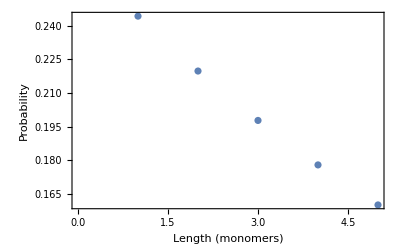

```mathematica
ListPlot[sslevels/.{koff->10,kon->9},Frame->True,FrameLabel->{"Length (monomers)","Probability"}]
```

Write this into a function

```mathematica
ssdist[nmax_]:=Block[{sslst,coeffs,sol1,p1ans},
{lst,ics,coeffs}=writeEqs[nmax];
sslst=lst/.p[_]'[t]->0;
sol1=Solve[sslst,Rest[coeffs]]//First;
p1ans=Solve[Total[coeffs/.sol1]==1,p[1][t]];
coeffs/.sol1/.p1ans//First]
```

```mathematica
ssplot=ssdist[25];
```

```mathematica
Manipulate[ListLinePlot[ssplot/.{koff->kf,kon->kn},PlotRange->{0,All},Frame->True,FrameLabel->{"Length (monomers)","Probability"}],{kn,.01,5},{kf,.01,5}]
```

## Is there are more efficient way to solve the ODEs? Try some linear algebra (section not finished)

```mathematica
{lst,ics,coeffs}=writeEqs[10];
{constmat,coeffmat}=Normal@CoefficientArrays[lst,coeffs];
```

```mathematica
MatrixForm[coeffmat]
```

(kon | -koff | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-kon | koff+kon | -koff | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -kon | koff+kon | -koff | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -kon | koff+kon | -koff | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -kon | koff+kon | -koff | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -kon | koff+kon | -koff | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -kon | koff+kon | -koff | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -kon | koff+kon | -koff | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -kon | koff+kon | -koff
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -kon | koff)

```mathematica
coeffinv=Inverse[coeffmat]
```

Inverse::sing: Matrix {{kon,-koff,0,0,0,0,0,0,0,0},{-kon,koff+kon,-koff,0,0,0,0,0,0,0},{0,-kon,koff+kon,-koff,0,0,0,0,0,0},{0,0,-kon,koff+kon,-koff,0,0,0,0,0},{0,0,0,-kon,koff+kon,-koff,0,0,0,0},{0,0,0,0,-kon,koff+kon,-koff,0,0,0},{0,0,0,0,0,-kon,koff+kon,-koff,0,0},{0,0,0,0,0,0,-kon,koff+kon,-koff,0},{0,0,0,0,0,0,0,-kon,koff+kon,-koff},{0,0,0,0,0,0,0,0,-kon,koff}} is singular.

Inverse[{{kon,-koff,0,0,0,0,0,0,0,0},{-kon,koff+kon,-koff,0,0,0,0,0,0,0},{0,-kon,koff+kon,-koff,0,0,0,0,0,0},{0,0,-kon,koff+kon,-koff,0,0,0,0,0},{0,0,0,-kon,koff+kon,-koff,0,0,0,0},{0,0,0,0,-kon,koff+kon,-koff,0,0,0},{0,0,0,0,0,-kon,koff+kon,-koff,0,0},{0,0,0,0,0,0,-kon,koff+kon,-koff,0},{0,0,0,0,0,0,0,-kon,koff+kon,-koff},{0,0,0,0,0,0,0,0,-kon,koff}}]

```mathematica
{eigs,vecs}=Eigensystem[coeffmat];
```

```mathematica
FullSimplify[eigs]
```

{0,koff+kon,koff+kon-1/2 (1+√5) √(koff kon),koff+kon+1/2 (1+√5) √(koff kon),koff+kon+√(koff kon) Root[5-5 #1^2+#1^4&,1],koff+kon+√(1/2 (5+√5)) √(koff kon),koff+kon+√(koff kon) Root[5-5 #1^2+#1^4&,2],koff+kon+(√(-(-5+√5) koff kon))/(√2),koff+kon-1/2 (-1+√5) √(koff kon),koff+kon+1/2 (-1+√5) √(koff kon)}

```mathematica
FullSimplify[vecs]
```

{{koff^9/kon^9,koff^8/kon^8,koff^7/kon^7,koff^6/kon^6,koff^5/kon^5,koff^4/kon^4,koff^3/kon^3,koff^2/kon^2,koff/kon,1},{-koff^4/kon^4,koff^4/kon^4,koff^3/kon^3,-koff^3/kon^3,-koff^2/kon^2,koff^2/kon^2,koff/kon,-koff/kon,-1,1},{koff^4/kon^4,(koff^3 (-2 koff+(1+√5) √(koff kon)))/(2 kon^4),-((1+√5) koff^3 (-kon+√(koff kon)))/(2 kon^4),-(koff^2 (koff+√5 koff-2 √(koff kon)))/(2 kon^3),-(koff kon)^(5/2)/kon^5,-(koff kon)^(3/2)/kon^3,-(koff (kon+√5 kon-2 √(koff kon)))/(2 kon^2),-((1+√5) (-koff+√(koff kon)))/(2 kon),-1+((1+√5) koff)/(2 √(koff kon)),1},{koff^4/kon^4,-(koff^3 (2 koff+(1+√5) √(koff kon)))/(2 kon^4),((1+√5) koff^3 (kon+√(koff kon)))/(2 kon^4),-(koff^2 (koff+√5 koff+2 √(koff kon)))/(2 kon^3),(koff kon)^(5/2)/kon^5,(koff kon)^(3/2)/kon^3,-(koff (kon+√5 kon+2 √(koff kon)))/(2 kon^2),((1+√5) (koff+√(koff kon)))/(2 kon),-1-((1+√5) koff)/(2 √(koff kon)),1},{-koff^4/kon^4,(koff^3 (2 koff-√(2 (5+√5)) √(koff kon)))/(2 kon^4),(koff^3 (-(3+√5) kon+√(2 (5+√5)) √(koff kon)))/(2 kon^4),(koff^2 ((3+√5) koff-2 √(5+2 √5) √(koff kon)))/(2 kon^3),((1+√5) koff^2 (-4 kon+√(2 (5+√5)) √(koff kon)))/(4 kon^3),-((1+√5) koff (-4 koff+√(2 (5+√5)) √(koff kon)))/(4 kon^2),(koff (-2 (3+√5) kon+4 √(5+2 √5) √(koff kon)))/(4 kon^2),((3+√5) koff-√(2 (5+√5)) √(koff kon))/(2 kon),-1+(√(1/2 (5+√5)) koff)/(√(koff kon)),1},{-koff^4/kon^4,(koff^3 (2 koff+√(2 (5+√5)) √(koff kon)))/(2 kon^4),-(koff^3 ((3+√5) kon+√(2 (5+√5)) √(koff kon)))/(2 kon^4),(koff^2 ((3+√5) koff+2 √(5+2 √5) √(koff kon)))/(2 kon^3),-((1+√5) koff^2 (4 kon+√(2 (5+√5)) √(koff kon)))/(4 kon^3),((1+√5) koff (4 koff+√(2 (5+√5)) √(koff kon)))/(4 kon^2),-(koff ((3+√5) kon+2 √(5+2 √5) √(koff kon)))/(2 kon^2),((3+√5) koff+√(2 (5+√5)) √(koff kon))/(2 kon),-1-(√(1/2 (5+√5)) koff)/(√(koff kon)),1},{-koff^4/kon^4,(koff^3 (2 koff-√2 √(-(-5+√5) koff kon)))/(2 kon^4),(koff^3 ((-3+√5) kon+√2 √(-(-5+√5) koff kon)))/(2 kon^4),(koff^2 (-2 (-3+√5) koff+4 √(5-2 √5) √(koff kon)))/(4 kon^3),-((-1+√5) koff^2 (-4 kon+√2 √(-(-5+√5) koff kon)))/(4 kon^3),((-1+√5) koff (-4 koff+√2 √(-(-5+√5) koff kon)))/(4 kon^2),(koff ((-3+√5) kon-2 √(5-2 √5) √(koff kon)))/(2 kon^2),-((-3+√5) koff+√2 √(-(-5+√5) koff kon))/(2 kon),-1+(√(-(-5+√5) koff kon))/(√2 kon),1},{-koff^4/kon^4,(koff^3 (2 koff+√2 √(-(-5+√5) koff kon)))/(2 kon^4),(koff^3 ((-3+√5) kon-√2 √(-(-5+√5) koff kon)))/(2 kon^4),-(koff^2 ((-3+√5) koff+2 √(5-2 √5) √(koff kon)))/(2 kon^3),((-1+√5) koff^2 (4 kon+√2 √(-(-5+√5) koff kon)))/(4 kon^3),-((-1+√5) koff (4 koff+√2 √(-(-5+√5) koff kon)))/(4 kon^2),(koff ((-3+√5) kon+2 √(5-2 √5) √(koff kon)))/(2 kon^2),(-(-3+√5) koff+√2 √(-(-5+√5) koff kon))/(2 kon),-1+(koff Root[5-5 #1^2+#1^4&,2])/(√(koff kon)),1},{koff^4/kon^4,(koff^3 (-2 koff+(-1+√5) √(koff kon)))/(2 kon^4),-((-1+√5) koff^3 (kon+√(koff kon)))/(2 kon^4),(koff^2 ((-1+√5) koff-2 √(koff kon)))/(2 kon^3),(koff kon)^(5/2)/kon^5,(koff kon)^(3/2)/kon^3,-(koff (kon-√5 kon+2 √(koff kon)))/(2 kon^2),-((-1+√5) (koff+√(koff kon)))/(2 kon),-1+((-1+√5) koff)/(2 √(koff kon)),1},{koff^4/kon^4,-(koff^3 (2 koff+(-1+√5) √(koff kon)))/(2 kon^4),((-1+√5) koff^3 (-kon+√(koff kon)))/(2 kon^4),(koff^2 ((-1+√5) koff+2 √(koff kon)))/(2 kon^3),-(koff kon)^(5/2)/kon^5,-(koff kon)^(3/2)/kon^3,(koff ((-1+√5) kon+2 √(koff kon)))/(2 kon^2),((-1+√5) (-koff+√(koff kon)))/(2 kon),-1-((-1+√5) koff)/(2 √(koff kon)),1}}